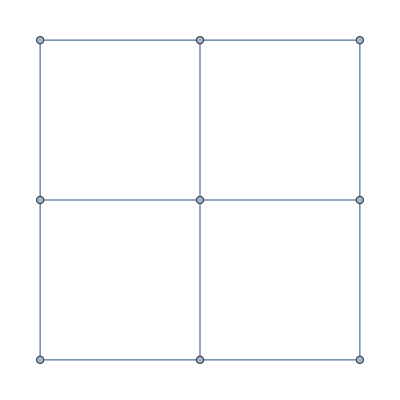

```mathematica
gridGraph=GridGraph[{3,3}]
```



```mathematica
Graphics[RegularPolygon[4]]
```

```mathematica
RegionBoundary[RegularPolygon[4]]
```

Line[{{1/(√2),-1/(√2)},{1/(√2),1/(√2)},{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)},{1/(√2),-1/(√2)}}]

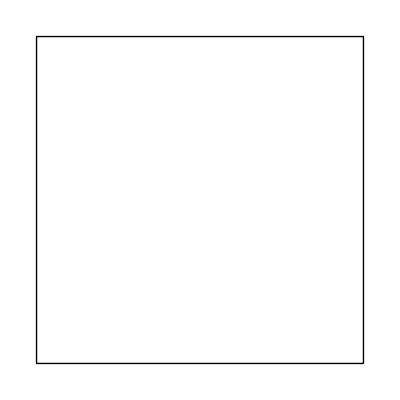

```mathematica
Graphics[RegionBoundary[RegularPolygon[4]]]
```

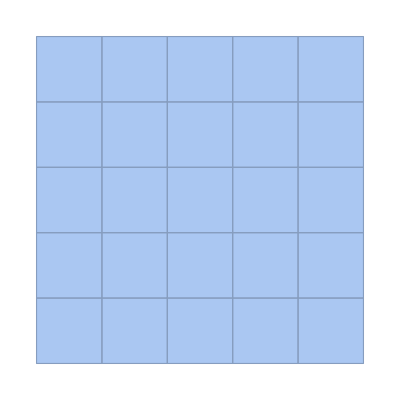

```mathematica
ArrayMesh[ConstantArray[1,{5,5}]]
```

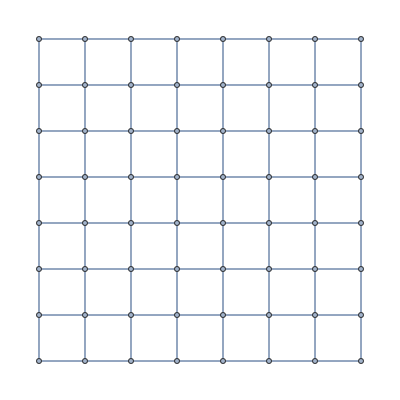

```mathematica
GridGraph[{8,8}]
```

```mathematica
ArrayMesh[ConstantArray[1,{5,5}]]
```

-Graphics-

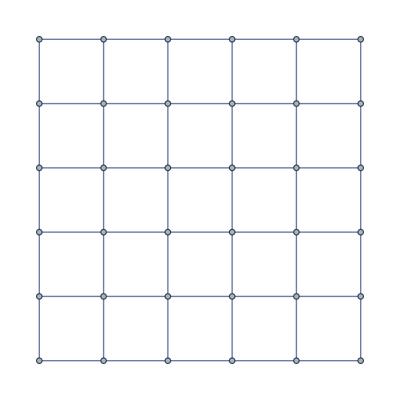

```mathematica
MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{5,5}]]]
```

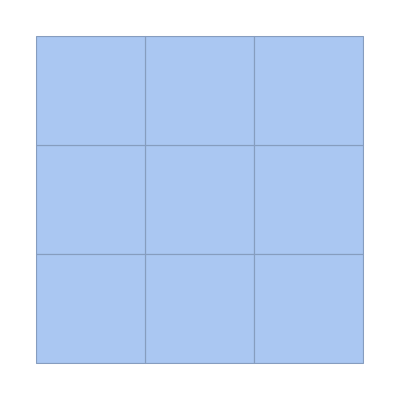

```mathematica
ArrayMesh[ConstantArray[1,{3,3}]]
```

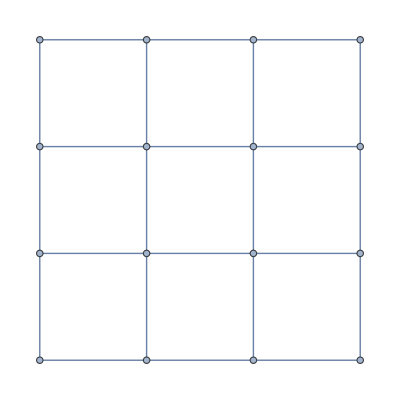

```mathematica
MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{3,3}]]]
```

```mathematica
IsomorphicGraphQ[MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{3,3}]]],GridGraph[{4,4}]]
```

True

```mathematica
mesh=ArrayMesh[ConstantArray[1,{5,5}]]
```

-Graphics-

```mathematica
MeshPrimitives[mesh,2]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
centroids=RegionCentroid/@MeshPrimitives[mesh,2]
```

{{0.5,4.5},{1.5,4.5},{2.5,4.5},{3.5,4.5},{4.5,4.5},{0.5,3.5},{1.5,3.5},{2.5,3.5},{3.5,3.5},{4.5,3.5},{0.5,2.5},{1.5,2.5},{2.5,2.5},{3.5,2.5},{4.5,2.5},{0.5,1.5},{1.5,1.5},{2.5,1.5},{3.5,1.5},{4.5,1.5},{0.5,0.5},{1.5,0.5},{2.5,0.5},{3.5,0.5},{4.5,0.5}}

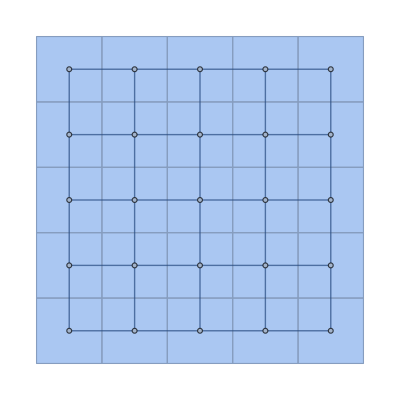

```mathematica
Show[{mesh,MeshConnectivityGraph[mesh,2,VertexCoordinates->centroids]}]
```

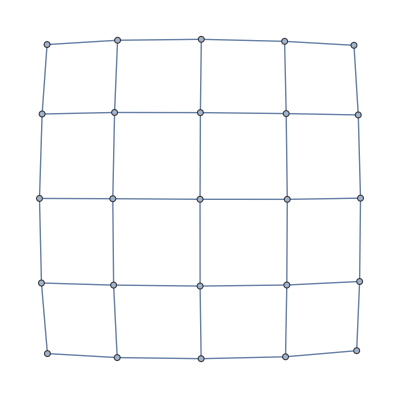

```mathematica
MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{5,5}]],2]
```

Use MeshConnectivityGraphpaclet:ref/MeshConnectivityGraph to test whether a mesh is connected:

```mathematica
ConnectedMeshQ[mesh_?MeshRegionQ]:=ConnectedGraphQ[MeshConnectivityGraph[mesh,0,RegionDimension[mesh]]]
```

```mathematica
Table[ConnectedMeshQ[i],{i,{-Graphics-,-Graphics3D-,-Graphics-, -Graphics-}}]
```

{False,True,True,True}

How do you go from a mesh connectivity graph to a mesh?

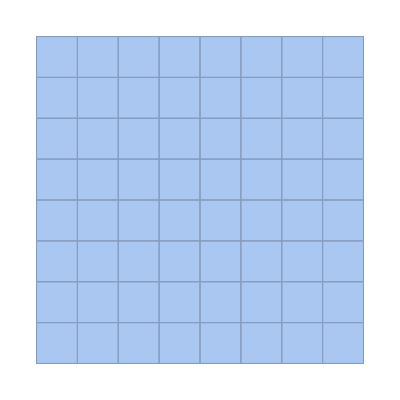

```mathematica
ArrayMesh[ConstantArray[1,{8,8}]]
```

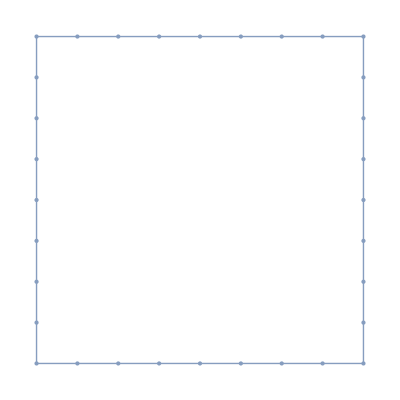

```mathematica
RegionBoundary[ArrayMesh[ConstantArray[1,{8,8}]]]
```

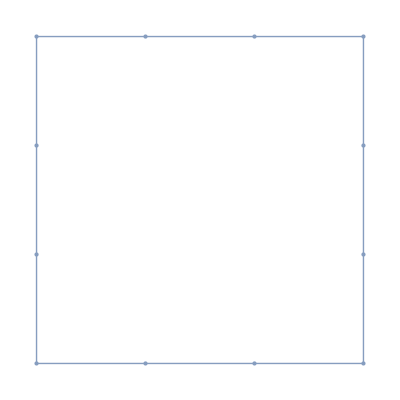

```mathematica
RegionBoundary[ArrayMesh[ConstantArray[1,{3,3}]]]
```

```mathematica
InputForm[RegionBoundary[ArrayMesh[ConstantArray[1,{3,3}]]]]
```

MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}]}]

```mathematica
MeshRegion[{{0.,0.},{0.,1.},{1.,0.},{0.,2.},{0.,3.},{1.,3.},{2.,0.},{2.,3.},{3.,0.},{3.,1.},{3.,2.},{3.,3.}},{Line[{{6,5},{5,4},{8,6},{11,12},{12,8},{4,2},{10,11},{2,1},{1,3},{3,7},{9,10},{7,9}}],Line[{0,1},{0,2}]}]
```

MeshRegion[{{0.,0.},{0.,1.},{1.,0.},{0.,2.},{0.,3.},{1.,3.},{2.,0.},{2.,3.},{3.,0.},{3.,1.},{3.,2.},{3.,3.}},{Line[{{6,5},{5,4},{8,6},{11,12},{12,8},{4,2},{10,11},{2,1},{1,3},{3,7},{9,10},{7,9}}],Line[{0,1},{0,2}]}]

```mathematica
MeshRegion[{{0.,0.},{0.,1.},{1.,0.},{0.,2.},{0.,3.},{1.,3.},{2.,0.},{2.,3.},{3.,0.},{3.,1.},{3.,2.},{3.,3.},{1,2},{1,3},{2,2},{2,3}},{Line[{{6,5},{5,4},{8,6},{11,12},{12,8},{4,2},{10,11},{2,1},{1,3},{3,7},{9,10},{7,9}}],Line[{{1,2},{1,3}}]}]
```

-Graphics-

```mathematica
MeshRegion[{{0,0},{1,0},{2,0},{3,0}},{Line[{{1,0},{2,0}}],Line[{{3,0},{4,0}}]}]
```

MeshRegion[{{0,0},{1,0},{2,0},{3,0}},{Line[{{1,0},{2,0}}],Line[{{3,0},{4,0}}]}]

```mathematica
MeshRegion[{{0,0},{1,0},{2,0},{3,0}}]
```

MeshRegion[{{0,0},{1,0},{2,0},{3,0}}]

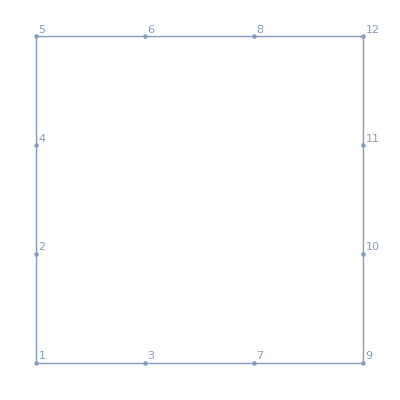

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}]}],Labeled[0,"Index"]]
```

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}]}],Labeled[0,"Index"]]
```

-Graphics-

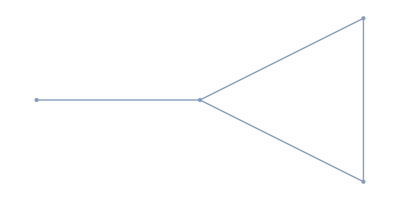

```mathematica
MeshRegion[{{0,0},{1,0},{2,1/2},{2,-1/2}},{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,2}]}]
```

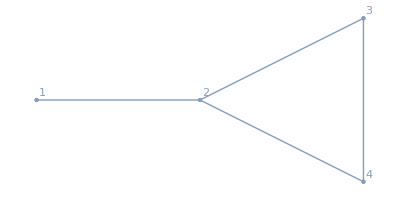

```mathematica
HighlightMesh[MeshRegion[{{0,0},{1,0},{2,1/2},{2,-1/2}},{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,2}]}],Labeled[0,"Index"]]
```

```mathematica
HighlightMesh[MeshRegion[{{0,0},{1,0},{2,1/2},{2,-1/2},{1,1}},{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,2}]}],Labeled[0,"Index"]]
```

-Graphics-

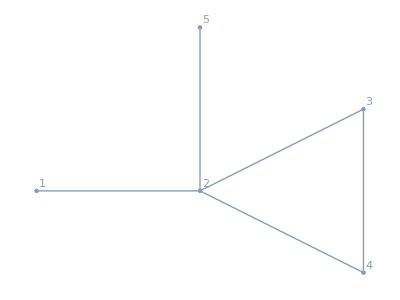

```mathematica
HighlightMesh[MeshRegion[{{0,0},{1,0},{2,1/2},{2,-1/2},{1,1}},{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,2}],Line[{5,2}]}],Labeled[0,"Index"]]
```

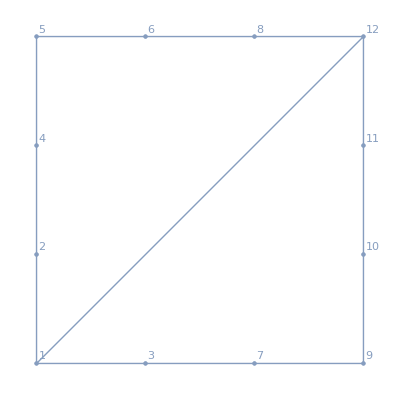

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{1,12}}]}],Labeled[0,"Index"]]
```

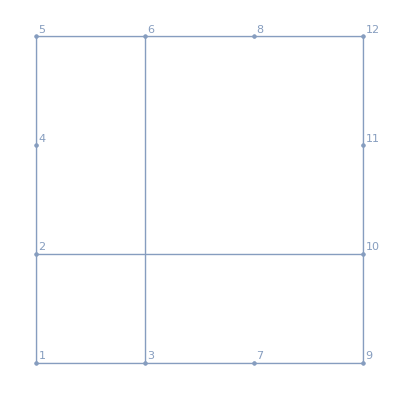

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{3,6}}],Line[{2,10}]}],Labeled[0,"Index"]]
```

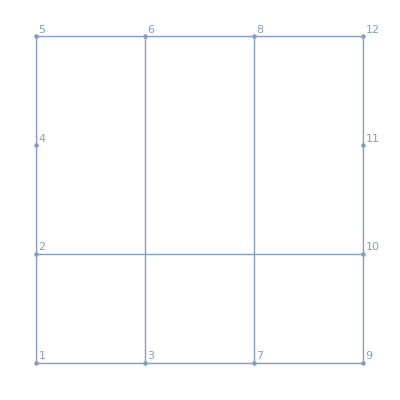

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{3,6}}],Line[{2,10}],Line[{7,8}]}],Labeled[0,"Index"]]
```

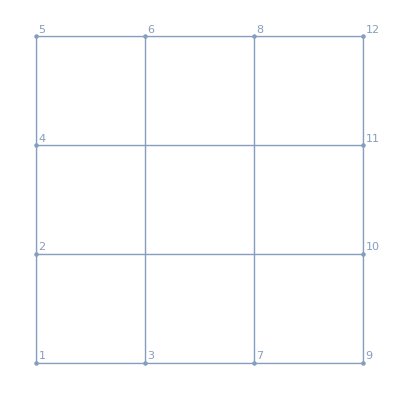

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{3,6}}],Line[{2,10}],Line[{7,8}],Line[{4,11}]}],Labeled[0,"Index"]]
```

```mathematica
Length[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{0,2}}]
```

13

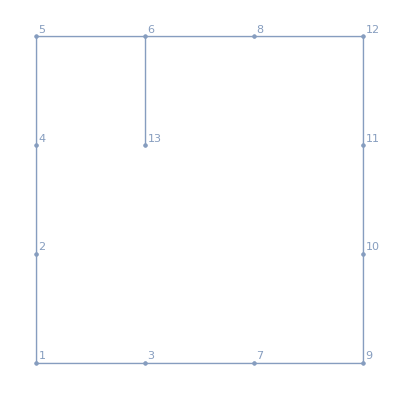

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6}}]}],Labeled[0,"Index"]]
```

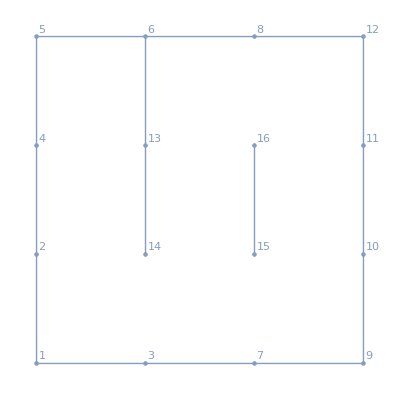

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15}}]}],Labeled[0,"Index"]]
```

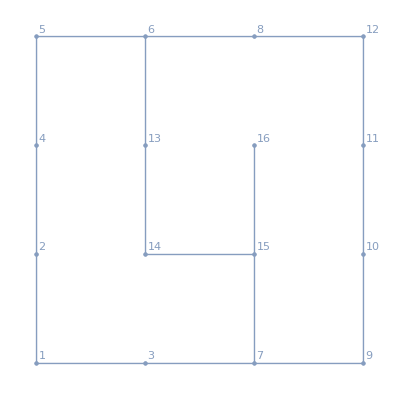

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15},{15,14},{15,7}}]}],Labeled[0,"Index"]]
```

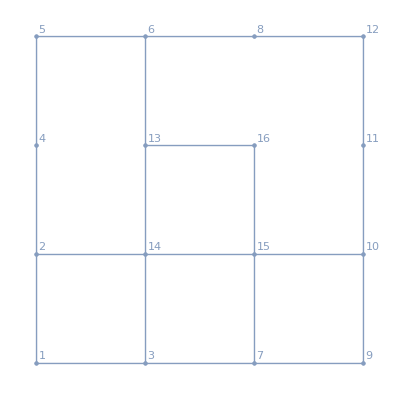

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15},{15,14},{15,7},{14,3},{14,2},{13,16},{15,10}}]}],Labeled[0,"Index"]]
```

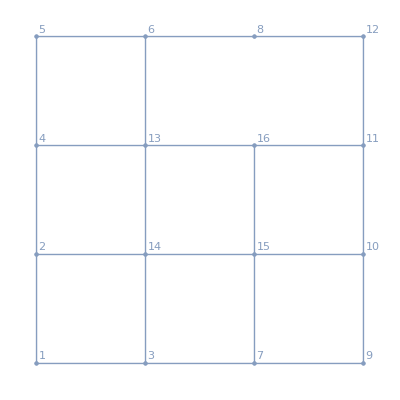

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15},{15,14},{15,7},{14,3},{14,2},{13,16},{15,10},{4,13},{16,11}}]}],Labeled[0,"Index"]]
```

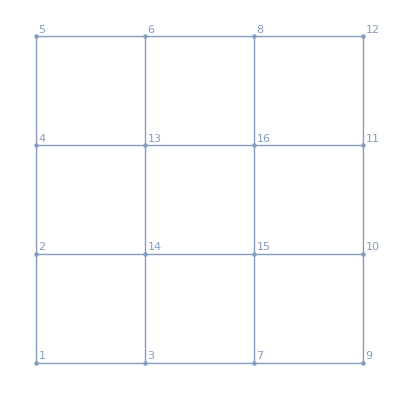

```mathematica
HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15},{15,14},{15,7},{14,3},{14,2},{13,16},{15,10},{4,13},{16,11},{16,8}}]}],Labeled[0,"Index"]]
```

```mathematica
mesh=HighlightMesh[MeshRegion[{{0., 0.}, {0., 1.}, {1., 0.}, {0., 2.}, 
 {0., 3.}, {1., 3.}, {2., 0.}, {2., 3.}, {3., 0.}, 
 {3., 1.}, {3., 2.}, {3., 3.},{1,2},{1,1},{2,1},{2,2}}, 
 {Line[{{6, 5}, {5, 4}, {8, 6}, {11, 12}, {12, 8}, 
   {4, 2}, {10, 11}, {2, 1}, {1, 3}, {3, 7}, {9, 
   10}, {7, 9}}],Line[{{13,6},{14,13},{16,15},{15,14},{15,7},{14,3},{14,2},{13,16},{15,10},{4,13},{16,11},{16,8}}]}],Labeled[0,"Index"]]
```

-Graphics-

```mathematica
MeshPrimitives[mesh,2]
```

{}

```mathematica
Table[{j,k},{k,0,3},{j,0,3}]
```

{{{0,0},{1,0},{2,0},{3,0}},{{0,1},{1,1},{2,1},{3,1}},{{0,2},{1,2},{2,2},{3,2}},{{0,3},{1,3},{2,3},{3,3}}}

```mathematica
Flatten[Table[{j,k},{k,0,3},{j,0,3}]]
```

{0,0,1,0,2,0,3,0,0,1,1,1,2,1,3,1,0,2,1,2,2,2,3,2,0,3,1,3,2,3,3,3}

```mathematica
Flatten[Table[{j,k},{k,0,3},{j,0,3}],{2}]
```

{{{0,0},{0,1},{0,2},{0,3}},{{1,0},{1,1},{1,2},{1,3}},{{2,0},{2,1},{2,2},{2,3}},{{3,0},{3,1},{3,2},{3,3}}}

```mathematica
Flatten[Table[{j,k},{k,0,3},{j,0,3}],{1}]
```

{{{0,0},{1,0},{2,0},{3,0}},{{0,1},{1,1},{2,1},{3,1}},{{0,2},{1,2},{2,2},{3,2}},{{0,3},{1,3},{2,3},{3,3}}}

```mathematica
Catenate[Table[{j,k},{k,0,3},{j,0,3}]]
```

{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{3,3}}

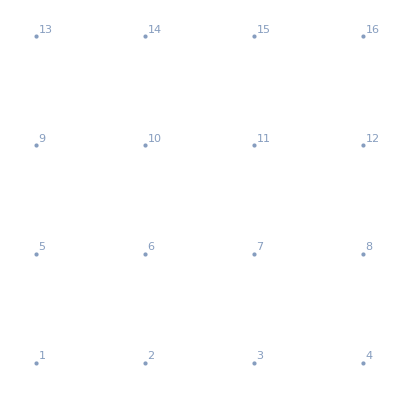

```mathematica
HighlightMesh[MeshRegion[Catenate[Table[{j,k},{k,0,3},{j,0,3}]], 
 {}],Labeled[0,"Index"]]
```

It seems the names are transposed. The mesh has the 2 in the lower right and the 5 in the upper left of the first square. The graph’s first square has 2 in the upper left and 5 in the lower right.

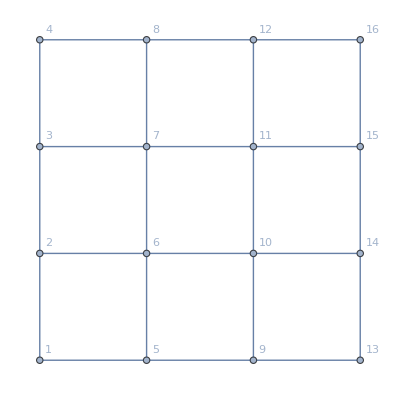

```mathematica
GridGraph[{4,4},VertexLabels->Automatic]
```

I found a way to fix it. Now the 2 is the upper left and the 5 is in the lower right of the graph.

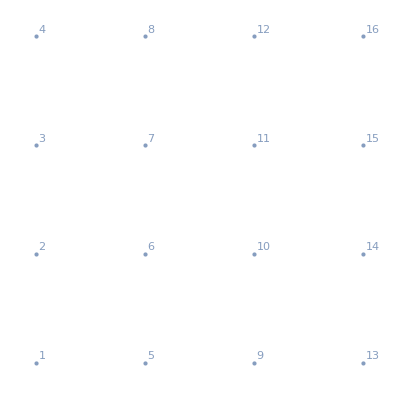

```mathematica
HighlightMesh[MeshRegion[Catenate[Table[{k,j},{k,0,3},{j,0,3}]], 
 {}],Labeled[0,"Index"]]
```

```mathematica
ArrayMesh[ConstantArray[1,{5,5}]]
```

-Graphics-

```mathematica
MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{5,5}]]]
```

-Graphics-

```mathematica
IsomorphicGraphQ[MeshConnectivityGraph[ArrayMesh[ConstantArray[1,{5,5}]]],GridGraph[{6,6}]]
```

True

It seems we just need to make a slightly bigger graph.

```mathematica
mazeBase=GridGraph[{8,8}]
```

-Graphics-

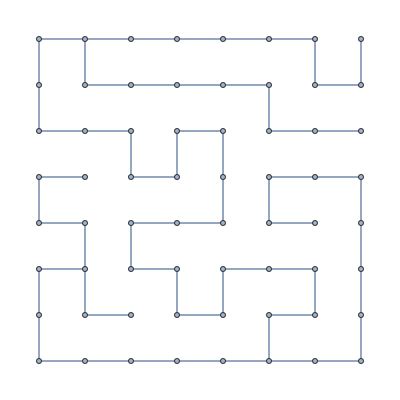

```mathematica
maze=MakeMaze[mazeBase]
```

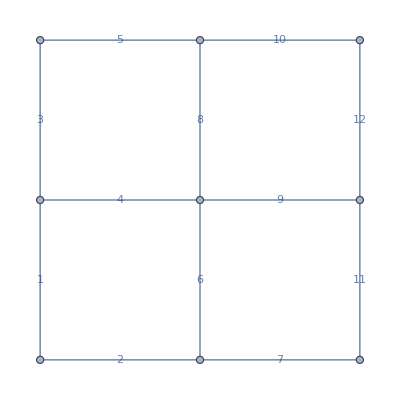

```mathematica
GridGraph[{3,3},EdgeLabels->"Index"]
```

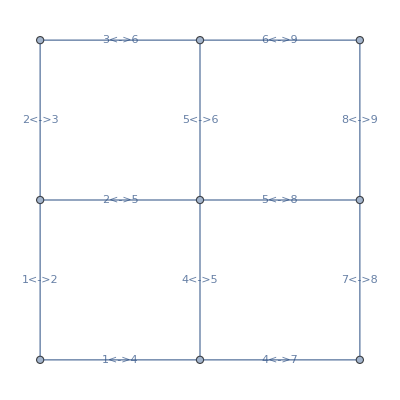

```mathematica
GridGraph[{3,3},EdgeLabels->"Name"]
```

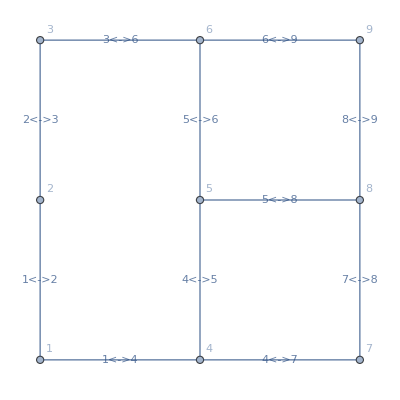

```mathematica
EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5},VertexLabels->Automatic]
```

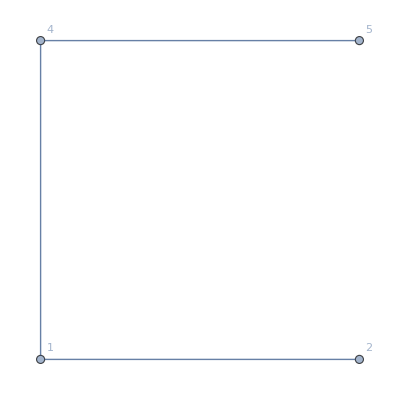

```mathematica
Graph[{1<->4,2<->1,4<->5,},GraphLayout->"GridEmbedding",VertexLabels->Automatic]
```

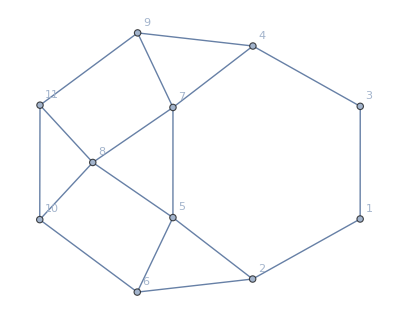

```mathematica
LineGraph[EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5}]]
```

```mathematica
DualPlanarGraph[EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5}]]
```

-Graphics-

```mathematica
IsomorphicSubgraphQ[DualPlanarGraph[EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5}]],GridGraph[{4,4}]]
```

False

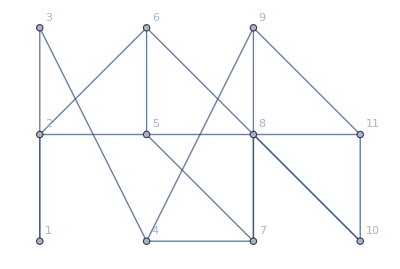

```mathematica
Graph[LineGraph[EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5}]],GraphLayout->"GridEmbedding"]
```

```mathematica
IsomorphicSubgraphQ[Graph[LineGraph[EdgeDelete[GridGraph[{3,3},EdgeLabels->"Name"],{2<->5}]],GraphLayout->"GridEmbedding"],GridGraph[{4,4}]]
```

False

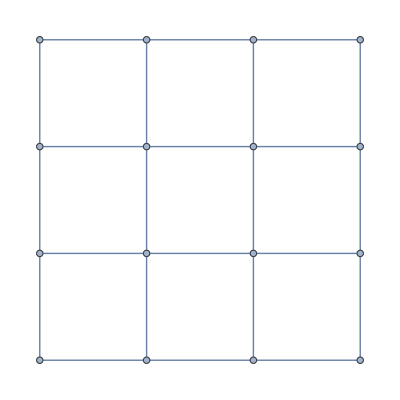

```mathematica
GridGraph[{4,4}]
```

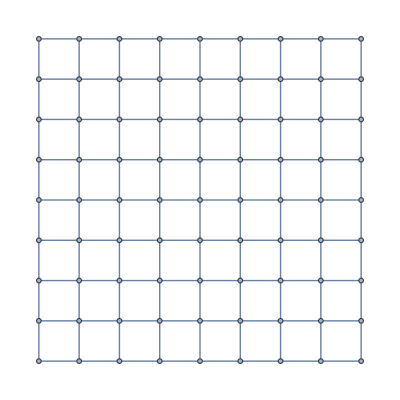

```mathematica
connectivityGraph=GridGraph[{9,9}]
```

## BoundaryMeshRegion documentation Applications examples

#### rectangle with holes

Build a BoundaryMeshRegionpaclet:ref/BoundaryMeshRegion in 2D with multiple rectangular holes. The coordinates for the inner rectangles:

```mathematica
rectangleCoords[{i_,j_}]:=rectangleCoords[{i,j},{0.5,0.5}];
rectangleCoords[{i_,j_},{α_,β_}]:={{i-α/2,j-β/2},{i+α/2,j-β/2},{i+α/2,j+β/2},{i-α/2,j+β/2}};
```

The indexes for the inner rectangle closed curves:

```mathematica
rectangleIndexes[i_]:=Line[i-1+{1,2,3,4,1}];
```

Generating an outer rectangle with m×n inner rectangle closed curves:

```mathematica
RectangleHoleMesh[{m_,n_}]:=
Module[{oc,hc},
hc=Flatten[Table[rectangleCoords[{i,j}],{j,n},{i,m}],2];
oc={{0,0},{m+1,0},{m+1,n+1},{0,n+1}};
BoundaryMeshRegion[Join[hc,oc],
rectangleIndexes[4 m n+1],
Sequence@@Table[rectangleIndexes[i],{i,1,4 m n,4}]
]
]
```

The resulting mesh can be used for computing:

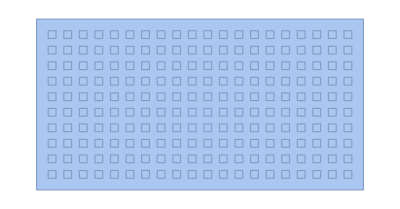

```mathematica
RectangleHoleMesh[{20,10}]
```

```mathematica
RegionMeasure[%]
```

181.

```mathematica
NumberForm[181.,16]
```

181.

#### regular polygons

```mathematica
RegularPolygonMesh[n_Integer?IntegerQ]:=BoundaryMeshRegion[CirclePoints[{0,0},{1,0},n],Line[Append[Range[n],1]]]
```

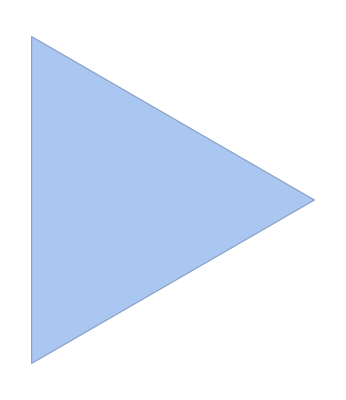
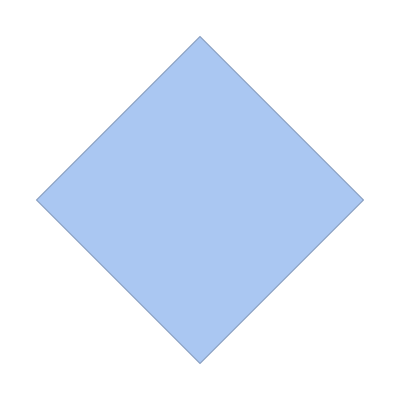
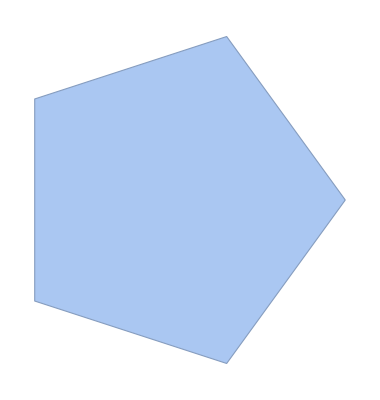
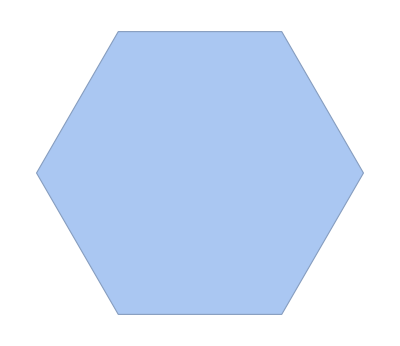
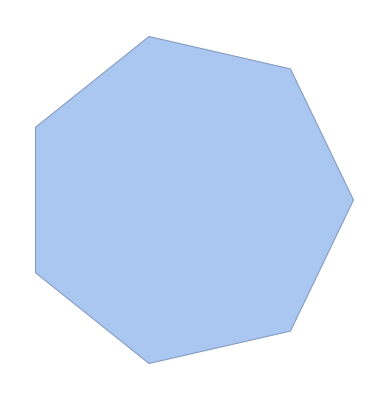
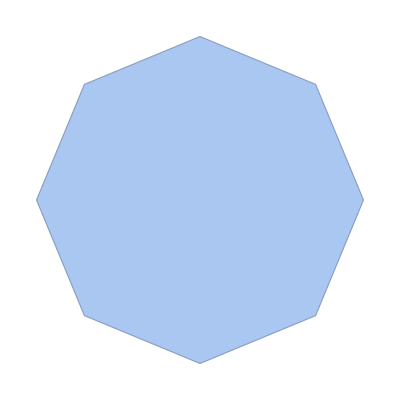
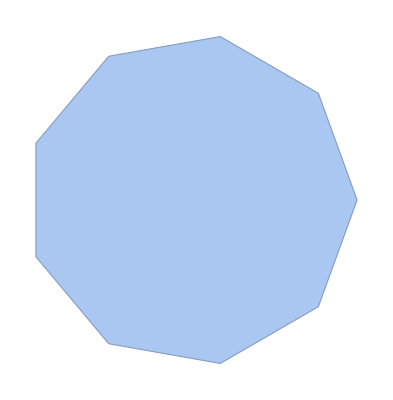
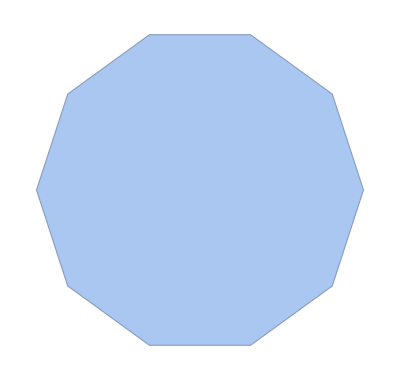

```mathematica
Table[RegularPolygonMesh[n],{n,3,10}]
```

The resulting regions can be used for computing:

```mathematica
Area/@()
```

{1.29904,2.,2.37764,2.59808,2.73641,2.82843,2.89254,2.93893}

The area approaches π as the number of sides goes to infinity:

```mathematica
Table[Area[RegularPolygonMesh[n]],{n,{10,10^2,10^3}}]
```

{2.93893,3.13953,3.14157}

```mathematica
With[{n=3},Table[{Cos[k 2π/n],Sin[k 2π/n]},{k,n}]]
```

{{-1/2,(√3)/2},{-1/2,-(√3)/2},{1,0}}

```mathematica
With[{n=3},Line[Append[Range[n],1]]]
```

Line[{1,2,3,1}]

```mathematica
CirclePoints[3]
```

{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}

```mathematica
Point[CirclePoints[3]]
```

Point[{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}]

```mathematica
Graphics[Point[CirclePoints[3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,π},3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,-π},3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,-π/2},3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,(3π)/2},3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,2π},3]]]
```

-Graphics-

```mathematica
Graphics[Point[CirclePoints[{1,0},3]]]
```

-Graphics-

```mathematica
CirclePoints[{1,0},3]
```

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2}}

```mathematica
CirclePoints[{3,3},{1,0},3]
```

{{4,3},{5/2,3+(√3)/2},{5/2,3-(√3)/2}}

```mathematica
Graphics[Point[CirclePoints[{3,3},{1,0},3]]]
```

-Graphics-

I didn’t realize you could specify the center of the circle, the radius, and the number of points.

```mathematica
CirclePoints[{3,3},{1,0},3]
```

{{4,3},{5/2,3+(√3)/2},{5/2,3-(√3)/2}}

It might be a good idea to add an option to modify the radius and the three sphere axis with SpherePoints and also rotate the ellipsoid and specify the angle to start from.

## MeshRegion documentation Applications examples

Convert a graph to a MeshRegionpaclet:ref/MeshRegion:

```mathematica
GraphMesh[g_?GraphQ]:=
MeshRegion[GraphEmbedding[g],Line[{##}]&@@@EdgeList[UndirectedGraph[g]]]
```

Some 2D embedded graphs:

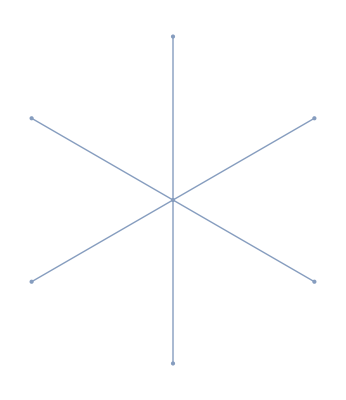
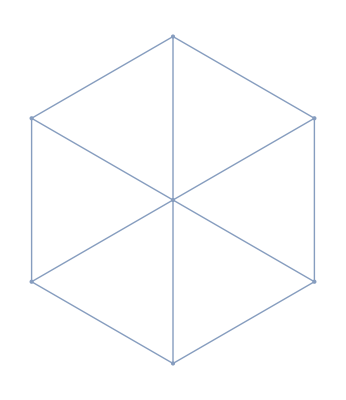
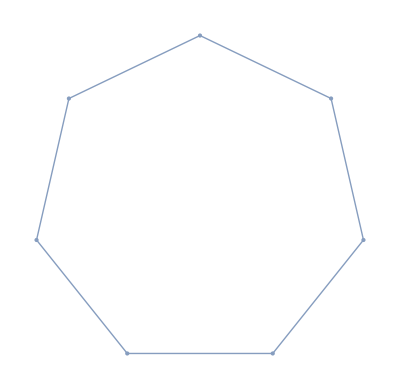
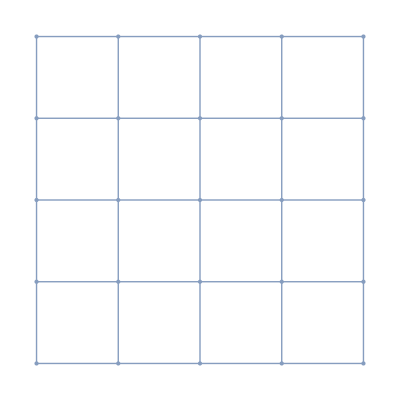
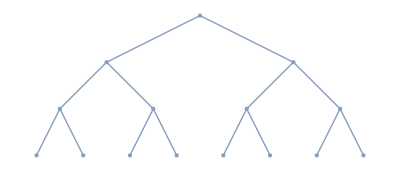

```mathematica
GraphMesh/@{StarGraph[7],WheelGraph[7],CycleGraph[7],GridGraph[{5,5}],CompleteKaryTree[4]}
```

You can compute with these as geometric regions:

```mathematica
ArcLength/@%
```

{6.,12.,6.07437,40.,13.4868}

```mathematica
Round/@ArcLength/@GraphMesh/@{StarGraph[7],WheelGraph[7],CycleGraph[7],GridGraph[{5,5}],CompleteKaryTree[4]}
```

{6,12,6,40,13}

Some 3D embedded graphs:

```mathematica
GraphMesh/@Graph3D/@{StarGraph[11],CycleGraph[7],GridGraph[{5,5,5}],CompleteKaryTree[4]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

You can still compute with them:

```mathematica
ArcLength/@%
```

{10.,6.07437,298.276,13.4868}

```mathematica
Round/@ArcLength/@GraphMesh/@Graph3D/@{StarGraph[11],CycleGraph[7],GridGraph[{5,5,5}],CompleteKaryTree[4]}
```

{10,6,298,13}

You can, for instance, compute the curve integral across these curves:

```mathematica
NIntegrate[x^2 y^2 z^2,{x,y,z}∈-Graphics3D-]
```

156061.

```mathematica
Round[NIntegrate[x^2 y^2 z^2,{x,y,z}∈-Graphics3D-]]
```

156061

```mathematica
Integrate[x^2 y^2 z^2,{x,y,z}∈-Graphics3D-]
```

156061.

```mathematica
Round[Integrate[x^2 y^2 z^2,{x,y,z}∈-Graphics3D-]]
```

156061

```mathematica
LineIntegrate[x^2 y^2 z^2,{x,y,z}∈GraphMesh[Graph3D[WheelGraph[7]]]]
```

Discrete`NLineIntegrateDump`$IntegrateFailed

```mathematica
LineIntegrate[x^2 y^2 z^2,{x,y,z}∈GraphMesh[Graph3D[WheelGraph[7]]],Direction->Automatic]
```

Discrete`NLineIntegrateDump`$IntegrateFailed

Shouldn’t this work?

```mathematica
RegionDimension[GraphMesh[Graph3D[WheelGraph[7]]]]
```

1

If its a line, why won’t LineIntegrate work?

```mathematica
RegionQ[GraphMesh[Graph3D[WheelGraph[7]]]]
```

True

The scalar line integral is independent of the parametrization and orientation of the curve. Any one dimensional RegionQpaclet:ref/RegionQ object can be used as curve.

It doesn’t work even though its a one-dimensional region with RegionQ true.

I think this is a bug. Either the documentation needs to explain why this doesn’t work, or it should have worked and there’s a bug in the kernel.

### surfaces

Create a surface mesh by extruding a 2D curve mesh:

```mathematica
GraphSurfaceMesh[g_?GraphQ]:=
RegionProduct[MeshRegion[GraphEmbedding[g],Line[{##}]&@@@EdgeList[UndirectedGraph[g]]],MeshRegion[{{0},{1}},Line[{1,2}]]]
```

Some examples with planar layouts:

```mathematica
GraphSurfaceMesh/@{StarGraph[7],WheelGraph[7],CycleGraph[7],GridGraph[{5,5}],CompleteKaryTree[4]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

You can compute with the resulting regions, in this case computing surface integrals:

```mathematica
NIntegrate[x^2 y^2 z^2,{x,y,z}∈-Graphics3D-]
```

0.225

```mathematica
RegionQ[-Graphics3D-]
```

True

```mathematica
RegionDimension[-Graphics3D-]
```

2

```mathematica
RegionEmbeddingDimension[-Graphics3D-]
```

3

```mathematica
RegionEmbeddingDimension[-Graphics3D-]-RegionDimension[-Graphics3D-]
```

1

```mathematica
RegionEmbeddingDimension[-Graphics3D-]-RegionDimension[-Graphics3D-]===1
```

True

Why does this not evaluate?

```mathematica
SurfaceIntegrate[x^2 y^2 z^2,-Graphics3D-]
```

SurfaceIntegrate[x^2 y^2 z^2,-Graphics3D-]

This is a bug.

The scalar surface integral is independent of the parametrization and orientation of the surface. Any n-1 dimensional RegionQpaclet:ref/RegionQ object in ℝ^n can be use for the surface.

Directly generate a rectangular grid mesh. Here IndexFlatten flattens out the position index in the same way that Flattenpaclet:ref/Flatten would flatten it:

```mathematica
IndexFlatten[i_List,d_List]:=1+FoldList[Times,1,Most[Reverse[d]]].Reverse[(i-1)]
```

```mathematica
GridMesh[{{l1_,l2_},{u1_,u2_}},{k1_,k2_}]:=
Module[{pa,ia,re},
pa=Table[{x,y},{x,l1,u1,(u1-l1)/k1},{y,l2,u2,(u2-l2)/k2}];
re={{1,1},{2,1},{2,2},{1,2}};
ia=Table[IndexFlatten[#,{k1,k2}+1]&/@TranslationTransform[{dx,dy}][re],{dx,0,k1-1},{dy,0,k2-1}];
MeshRegion[Flatten[pa,1],Polygon[Flatten[ia,1]]]
]
```

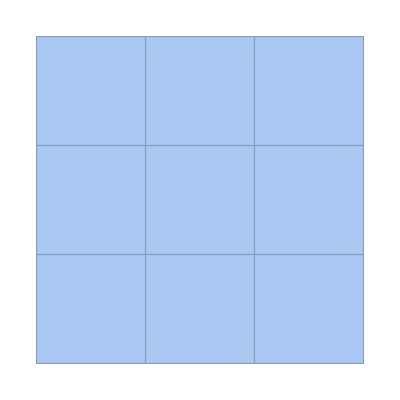

```mathematica
GridMesh[{{0,0},{1,1}},{3,3}]
```

Alternatively, generate the same mesh region as the product of 1D meshes:

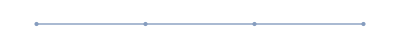

```mathematica
mr1d=MeshRegion[{{0},{1/3},{2/3},{1}},Line[{1,2,3,4}]]
```

```mathematica
RegionProduct[mr1d,mr1d]
```

-Graphics-

Generalize the direct method above to generate a mesh region corresponding to a pattern matrix:

```mathematica
IndexFlatten[i_List,d_List]:=1+FoldList[Times,1,Most[Reverse[d]]].Reverse[(i-1)]
```

```mathematica
PatternGridMesh[a_List]/;MatrixQ[a]:=
Module[{m,n,pa,ia,re},
{m,n}=Dimensions[a];
pa=Table[{x,y},{x,0,m},{y,0,n}];
re={{1,1},{2,1},{2,2},{1,2}};
ia=Table[IndexFlatten[#,{m,n}+1]&/@TranslationTransform[ind-1][re],{ind,Position[a,1]}];
MeshRegion[Flatten[pa,1],Polygon[ia]]
]
```

Some simple patterns:

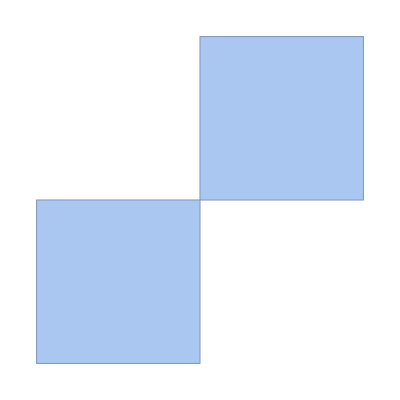

```mathematica
PatternGridMesh[{{1,0},{0,1}}]
```

More involved patterns:

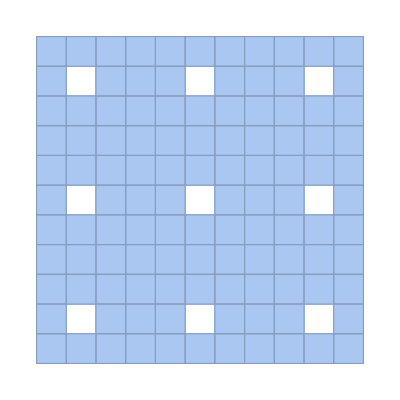

```mathematica
PatternGridMesh[Table[If[Mod[i,4]==2&&Mod[j,4]==2,0,1],{i,11},{j,11}]]
```

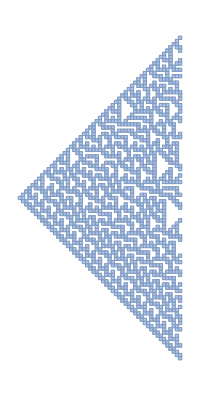

```mathematica
PatternGridMesh[CellularAutomaton[30,{{1},0},50]]
```

### volumes

Directly generate a rectangular grid mesh. Here IndexFlatten flattens out the position index in the same way that Flattenpaclet:ref/Flatten would flatten it:

```mathematica
IndexFlatten[i_List,d_List]:=1+FoldList[Times,1,Most[Reverse[d]]].Reverse[(i-1)]
```

```mathematica
GridMesh[{{l1_,l2_,l3_},{u1_,u2_,u3_}},{k1_,k2_,k3_}]:=
Module[{pa,ia,re},
pa=Table[{x,y,z},{x,l1,u1,(u1-l1)/k1},{y,l2,u2,(u2-l2)/k2},{z,l3,u3,(u3-l3)/k3}];
re={{1,1,1},{2,1,1},{2,2,1},{1,2,1},{1,1,2},{2,1,2},{2,2,2},{1,2,2}};
ia=Table[IndexFlatten[#,{k1,k2,k3}+1]&/@TranslationTransform[{dx,dy,dz}][re],{dx,0,k1-1},{dy,0,k2-1},{dz,0,k3-1}];
MeshRegion[Flatten[pa,2],Hexahedron[Flatten[ia,2]]]
]
```

```mathematica
GridMesh[{{0,0,0},{1,1,1}},{3,3,3}]
```

-Graphics3D-

Alternatively, generate the same mesh region as the product of 1D meshes:

```mathematica
mr1d=MeshRegion[{{0},{1/3},{2/3},{1}},Line[{1,2,3,4}]]
```

-Graphics-

```mathematica
RegionProduct[mr1d,mr1d,mr1d]
```

-Graphics3D-

Generalize the direct method above to generate a mesh region corresponding to a pattern matrix:

```mathematica
IndexFlatten[i_List,d_List]:=1+FoldList[Times,1,Most[Reverse[d]]].Reverse[(i-1)]
```

```mathematica
PatternGridMesh[a_List]/;ArrayQ[a]&&ArrayDepth[a]==3:=
Module[{m,n,p,pa,ia,re},
{m,n,p}=Dimensions[a];
pa=Table[{x,y,z},{x,0,m},{y,0,n},{z,0,p}];
re={{1,1,1},{2,1,1},{2,2,1},{1,2,1},{1,1,2},{2,1,2},{2,2,2},{1,2,2}};
ia=Table[IndexFlatten[#,{m,n,p}+1]&/@TranslationTransform[ind-1][re],{ind,Position[a,1]}];
MeshRegion[Flatten[pa,2],Hexahedron[ia]]
]
```

A simple pattern:

```mathematica
PatternGridMesh[{{{1,1,1},{1,0,1},{1,1,1}},
{{1,1,1},{1,0,1},{1,1,1}},{{1,1,1},{1,0,1},{1,1,1}}}]
```

-Graphics3D-

More involved patterns:

```mathematica
PatternGridMesh[CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},10]]
```

-Graphics3D-

Use the idea above to construct a Seidel mesh, i.e. a mesh region with tunnels going in every direction without crossing:

```mathematica
SeidelMesh[{r_,s_,t_}]:=
PatternGridMesh[Table[If[Mod[i,4]==2&&Mod[j,4]==2||Mod[i,4]==0&&Mod[k,4]==0||Mod[j,4]==0&&Mod[k,4]==2,0,1],{i,3+r 4},{j,3+s 4},{k,3+t 4}]]
```

```mathematica
SeidelMesh[{1,1,1}]
```

-Graphics3D-

By converting to a boundary mesh and styling it, it becomes easier to comprehend:

```mathematica
HighlightMesh[BoundaryMesh@SeidelMesh[{2,2,2}],{Style[1,None],Style[2,Opacity[0.5]]}]
```

-Graphics3D-

```mathematica
HighlightMesh[BoundaryMesh@SeidelMesh[{4,4,4}],{Style[1,None],Style[2,Opacity[0.5]]}]
```

-Graphics3D-

## Figuring out what to do

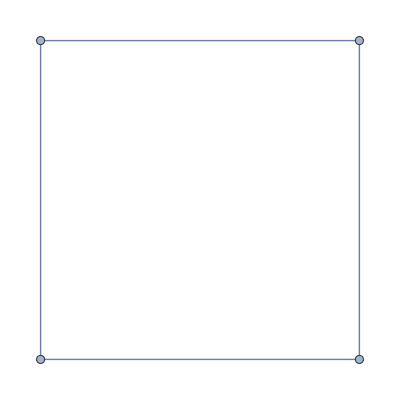

```mathematica
GridGraph[{2,2}]
```

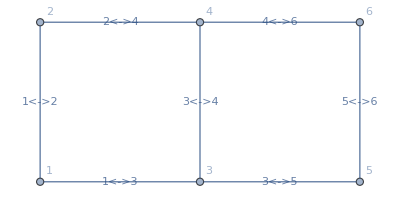

```mathematica
GridGraph[{2,3},VertexLabels->Automatic,EdgeLabels->Automatic]
```

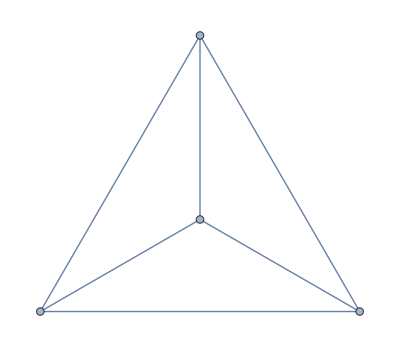

```mathematica
DualPlanarGraph[-Graphics-]
```

```mathematica
PlanarFaceList[-Graphics-]
```

{{1,2,3},{1,3,4},{1,4,2},{2,4,3}}

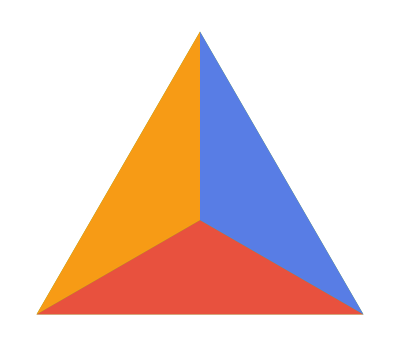

```mathematica
g=-Graphics-;

coloring=FindPlanarColoring[g,ColorData[106,"ColorList"]];Graphics[GraphicsComplex[GraphEmbedding[g],Reverse@Table[Style[Polygon[PlanarFaceList[g][[i]]],coloring[[i]]],{i,Length[coloring]}]]]
```

```mathematica
coloring
```

{RGBColor[0.34398, 0.49112, 0.89936],RGBColor[0.97, 0.606, 0.081],RGBColor[0.91, 0.318, 0.243],RGBColor[0.448, 0.69232, 0.1538]}

```mathematica
Last[PlanarFaceList[g]]
```

{2,4,3}

```mathematica
PlanarFaceList[g]
```

{{1,2,3},{1,3,4},{1,4,2},{2,4,3}}

```mathematica
Graph[CanonicalGraph[g],GraphLayout->"PlanarEmbedding",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphEmbedding[]
```